```mathematica
(*以下路径需要改成您电脑上txt的路径*)
(*您运行时可以将Export函数删去*)
```

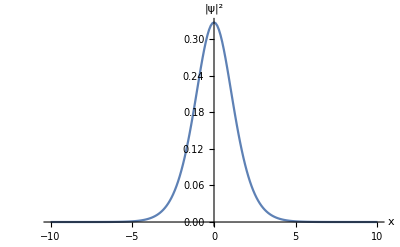

```mathematica
data0k=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业\\第三次大作业\\temp1.txt","Table"];
(*由于这函数衰减很快,这里只取-10~10的点进行展示*)
data0cut=Table[data0k[[i]],{i,16284,16484}];
show0=Show[ListLinePlot[data0cut],AxesLabel->{"x","|ψ|^2"}]
Export["big3I1.pdf",show0];
```

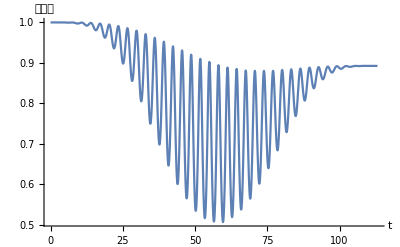

```mathematica
data=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业\\第三次大作业\\temp2_Pt.txt","Table"];
show1=Show[ListLinePlot[data],AxesLabel->{"t","布居数"}]
Export["big3I2_Pt.pdf",show1];
```

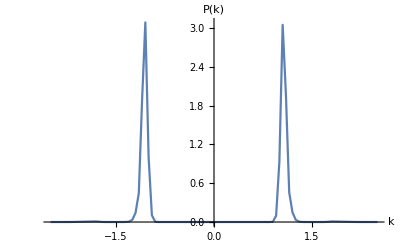

```mathematica
data2=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业\\第三次大作业\\temp2_k.txt","Table"];
show2=Show[ListLinePlot[data2,PlotRange->All],AxesLabel->{"k","P(k)"}]
Export["big3I2_k.pdf",show2];
```

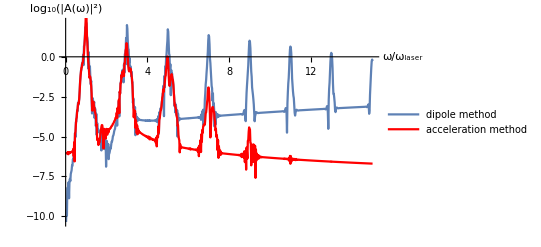

```mathematica
data3d=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业\\第三次大作业\\temp3_d.txt","Table"];
data3d=Table[data3d[[i]],{i,1,722}];
data3a=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业\\第三次大作业\\temp3_a.txt","Table"];
data3a=Table[data3a[[i]],{i,1,722}];
show3=Show[ListLinePlot[data3d,PlotRange->All,PlotLegends->{"dipole method"}],ListLinePlot[data3a,PlotRange->All,PlotStyle->Red,PlotLegends->{"acceleration method"}],AxesLabel->{"ω/ω_laser","log_10(|A(ω)|^2)"}]
Export["big3I3.pdf",show3];
```

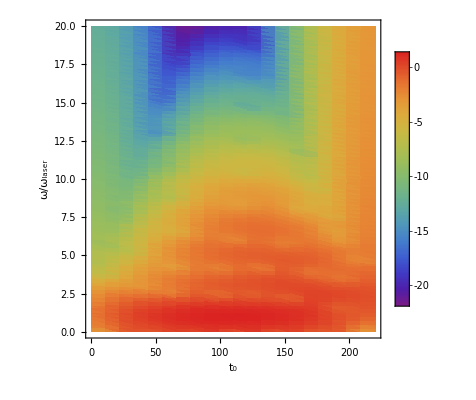

big3I4.pdf

```mathematica
data4=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业\\第三次大作业\\temp4.txt","Table"];
show4=Show[ListDensityPlot[data4,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"t_0","ω/ω_laser"}]]
Export["big3I4.pdf",show4]
```